# Direction Selectivity

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/mathieu/Copy/dendritic_tree3/OnlineAMPANegW/ForPaper

## Code

### Init

```mathematica
$HistoryLength=100;
```

### compilation Attributes

```mathematica
Const/: (a_Symbol = Const[b_]) :=
(a =b; SetAttributes[a,Protected]; b)
```

```mathematica
SetAttributes[InlComp,HoldAll];
InlComp[inls_,parms_,code_,decl_] :=
Block[ {curprot,Trans2Rule,r1,r2,rcode,a,cmp,t},

curprot := Block[ {t,a,s} ,
t = Names[$Context<>"*"];
a = Map[Attributes,t];
t=t[[ Map[First,Position[a,Protected,{2}]] ]];t= Map[ToExpression[#,StandardForm,Hold]&,t]
];

SetAttributes[Trans2Rule,HoldAll];
    Trans2Rule[sym_] := Block[ {t},
t = DownValues[sym];
If [Length[t] == 0,
{HoldPattern[sym] -> sym},
t]
];

SetAttributes[cmp,HoldAll];

r1  = Apply[Trans2Rule,curprot,{1}];
r2 = Map[Trans2Rule,Unevaluated@inls];
rcode = Hold[code] //. Flatten[{r1,r2}];
t=cmp[parms,rcode,decl] /. HoldPattern[rcode]-> rcode /. Hold[a___] -> a;
Compile@@t
]
```

```mathematica
GlobalRefs[f_CompiledFunction]:= Block[ {a,b},
Cases[
f[[4]], 
HoldPattern[Function[a_List, b___]] -> HoldForm[b],
∞
]
]
```

## set values

```mathematica
NN=100;
 
(* input dimension *)
Tmax = Const[100];  (* max. inputlength *)
step = 0.2; 
Tonl=Const[Tmax];(* τM in paper (for the elgibility trace low pass filter) *)
w = Table[1,{NN}]; (* no weight!!! *)
Urest = Const[-1] ;(* resting potential *)
(*α : factor of reduction of s^ν and Subscript[E, i] over one time step *)
α=N[1-step/Tonl];
(*β : factor of reduction of Subscript[e, i] over one time step *)
β=N[step/Tonl];
γ=N[1/Tonl];
(*invE : threshold for s^ν *)
tmr = 10.0; (* decay time of the reset kernel *)
tmrini =N[ 10/tmr]; (* constant to update resets of spiking neurons *)
tmrsfac=N[1-step/tmr]; (* factor of reduction of the reset kernel over one time step *)
rewdelay = 0.;(*delay for a reward *)
FlucLen =0; (* to modulate the pattern length *)
λ=1; (* smoothing factor for the exponential moving average *)
tNMDA=50//Const;(*duration of a NMDA spike *)
stNMDA= IntegerPart[tNMDA/step]; (* number of steps for a NMDA spike *)
stNMDAReal=1.0*stNMDA;(* number of steps for a NMDA spike *)
UspikeNMDA=0.3;
mu=0.1;
pConnect=0.5;(* connectivity probability *)
β2=5.;
βN=5.;
Umax=10.0//Const (*for the dendritic branches*);
UmaxSoma=2.//Const (*for the soma until le first order approx is quite correct*);
sigma=1.4;
pOff=0.2;
nbNeuron=40;
τfracSp=4;
msNumber=-Log[$MachineEpsilon *100.];
```

```mathematica
τs=1.5;τm=10.0;
```

```mathematica
Toverlap=25;
```

```mathematica
KN:=Round[Toverlap*(NN-1)/Tonl](* numer of neurons which fire with hight rate *)
```

```mathematica
fh=Const[100];
```

```mathematica
fl=5.;
```

```mathematica
UrestSoma=Const[-1];
```

```mathematica
cSpikeTime=Tonl/2;(* desired spike time *)
cSpikeTimeStep=cSpikeTime/step;(* desired spike time (number of step) *)
```

```mathematica
τfrac=0.5//Const (* fraction of time cte for the low pass filters *);
```

```mathematica
BoundSyn=1000;
```

```mathematica
k2=Const[0.006737946999085467];
```

```mathematica
LearnSpike=True;
```

```mathematica
aAMPA:=N[1./(2*nbNeuron)];
```

```mathematica
stepperlist=0;(* to keep the membrane potential in "stepper" *)
```

```mathematica
setStep[newStep_]:=(step=newStep;αg=N[1-step/Tonl];βg=N[step/Tonl];γg=N[1/Tonl];αl=N[1-step/tNMDA];βl=N[step/tNMDA];γl=N[1/tNMDA];tmrsfac=N[1-step/tmr];stNMDA= IntegerPart[tNMDA/step];stNMDAReal=1.0*stNMDA;);
```

```mathematica
setStep[step];
```

## Develop functions

### load packages

```mathematica
(* to write in the Messages windows *)
msg[expr_] := NotebookWrite[First@Notebooks["Messages"],
Cell[BoxData[MakeBoxes[expr,StandardForm]],"Output"]];
```

### define getFileName

```mathematica
getFileName[lstep_,trials_, opt_]:="./out/"<>"_eta"<>ToString[lstep//N]<>"_trials"<>ToString[trials]<>"_IL"<>ToString[NN]<>"_NbNeurons"<>ToString[nbNeuron]<>"_USpike"<>ToString[UspikeNMDA]<>"_SigmaW"<>ToString[σW]<>"_UrS"<>ToString[UrestSoma]<>"_aAMPA"<>ToString[aAMPA]<>"_Tolp"<>ToString[Toverlap]<>"_"<>opt<>".out"
```

### define postsynaptic and reset kernel

```mathematica
myeps[] := Block[ {tm = τm,ts=τs}, 
  (ⅇ^(-t/tm)-ⅇ^(-t/ts))/(tm-ts)]
```

```mathematica
myeta[]:= Block[ {tm = τm},
ⅇ^(-t/tm)/tm];
```

```mathematica
eps[t_] =myeps[];
SetAttributes[eps,Listable];
eta[t_] = 3myeta[];
SetAttributes[eta,Listable];
```

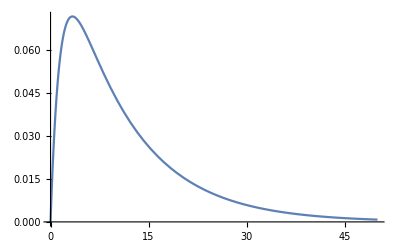

```mathematica
Plot[eps[t],{t,0,50}]
```

```mathematica
Integrate[eps[t],{t,0,∞}]
```

1.

### define stochastic intensity

```mathematica
(* escape noise for the dendrites *)
(*{ϕN,DϕN,DlϕN} = Block[ 
{k =100.(* firing at saturation *),β =5.0 (* Noise*),d =10000.0 (* shift factor*),dd,
f,df,dlf,u,kk,ββ ,a,b,c, cc},
f =  kk/(1+dd*Exp[-ββ*t]);
df =(kk*dd*ββ*Exp[-ββ*t])/(1+dd*Exp[-ββ*t])^2;
dlf = (ββ*dd)/(Exp[ββ*t]+dd);
{f,df,dlf} ={f,df,dlf}  /. {kk -> k,ββ ->  β,dd ->  d};
Map[ Function[ {t}, #]&, {a,b,c  +cc*t}]/. {a -> f, b-> df, c-> dlf,cc ->0.}
];*)
```

```mathematica
(* escape noise for the dendrites *)
{ϕN,DϕN,DlϕN} = Block[ 
{k =5.(* firing at saturation *),β =5.0 (* Noise*),d =1096.63 (* shift factor*),dd,
f,df,dlf,u,kk,ββ ,a,b,c, cc},
f =  kk/(1.0+dd*t);
df =(kk*dd*ββ*t)/(1.0+dd*t)^2;
dlf = (ββ*dd)/(1./t+dd);
{f,df,dlf} ={f,df,dlf}  /. {kk -> k,ββ ->  β,dd ->  d};
Map[ Function[ {t}, #]&, {a,b,c  +cc*t}]/. {a -> f, b-> df, c-> dlf,cc ->0.}
];
```

```mathematica
(* escape noise for the soma *)
{ϕS,DϕS,DlϕS} = Block[ 
{k =k2,β =β2,
f,df,dlf,u,kk,ββ ,a,b,c, cc},
f =  kk ⅇ^(ββ *t);
df =kk ββ ⅇ^(ββ *t);
dlf = (*df/f*)ββ;
{f,df,dlf} ={f,df,dlf}  /. {kk -> k,ββ ->  β};
Map[ Function[ {t}, #]&, {a,b,c  +cc*t}]/. {a -> f, b-> df, c-> dlf,cc ->0.}
];
```

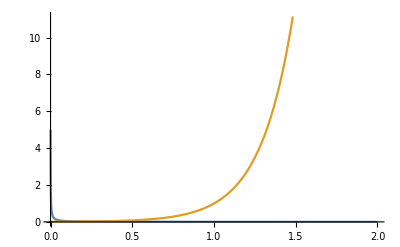

```mathematica
Plot[{ϕN[u],ϕS[u]},{u,0,2}]
```

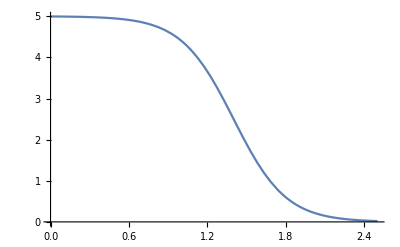

```mathematica
Plot[{DlϕN[Exp[-β2*u]]},{u,0,2.5}]
```

### define mempots

```mathematica
(* to calculate the membrane potential in the dendritic branchs *)
mempots[w_,inp_] := Block[ {tmp,us},
us=w.Transpose[inp]+Urest;
(*us= us* UnitStep[Umax-us]+Umax*UnitStep[us-Umax];*)(*saturation of the membrane potential at Umax *)
us
];
```

### define spikegenNMDA

```mathematica
(* spike or not with escape noise *)
spikegenNMDA[us_]:=
Block[{usf=Flatten[us],spikesi,t},
(*spikesi=Sign[step * ϕN[usf]-RandomReal[{0,1},Length[usf]]];*)
spikesi=Sign[1.-Exp[-step * ϕN[usf]]-RandomReal[{0,1},Length[usf]]];
If[Max[spikesi]≠1,{0},Flatten[Position[spikesi,1]]]
];
```

```mathematica
(* spike or not with escape noise *)
spikegenNMDA[us_,refPeriod_]:=
Block[{usf=Flatten[us],spikesi,t},
spikesi=Sign[step * ϕN[usf]*refPeriod-RandomReal[{0,1},Length[usf]]];If[Max[spikesi]≠1,{0},Flatten[Position[spikesi,1]]]
];
```

### define incrBuff

```mathematica
(* spike or not with escape noise *)
incrBuff[lindBuff_]:=
Block[{ind},
ind = Mod[lindBuff+1,stNMDA+1];
If[ind==0,1,ind]
];
```

### define myUnitStep

```mathematica
(Min[(tNMDA/(tNMDA+step)),Tonl/(Tonl+step)]+0.00001)/1000
```

0.000996026

```mathematica
myUnitStep[numb_]:=Block[{},
0.5*(Sign[(numb)+0.00099602593625498]+1.0)
];
```

### define ToFloat

```mathematica
ToFloat[numb_]:=Block[{numFl},
numFl=(numb*1.0);
numFl
];
```

### define SomaSat

```mathematica
SomaSat[u_]:=myUnitStep[UmaxSoma-u]u+myUnitStep[u-UmaxSoma]UmaxSoma;
```

### define spikegenPreSyn

```mathematica
(* spike or not with escape noise *)
spikegenPreSyn[rates_]:=
Block[{},
0.5*(Sign[1.-Exp[-(step/1000.(* rate in Hz and step in ms*)) * rates]-RandomReal[{0,1},Length[rates]]
]+1.)
];
```

### define stepper

```mathematica
stepper =
InlComp[
{mempots,spikegenNMDA,incrBuff,myUnitStep,ϕN,ϕS,k2,DϕN,DlϕN,DϕS,DlϕS,Tonl,step,stNMDA,tNMDA,β2,tmrsfac,αg,βg,γg,αl,βl,γl,τfrac,Urest,msNumber,UmaxSoma,SomaSat,τs,τm,spikegenPreSyn},
{{myinps,_Real,2},   (* input potentials *)
{myw,_Real,2},(* weights for the "dendritic neurons" and AMPA synapses for the first component*)
{resets,_Integer,1}, (* the NMDA spike response *)
{reset,_Real}, (* the reset kernel for the soma *)
{ETr,_Real,2}, (* the eligibility trace *)
{resets2,_Integer,1}, (* the NMDA spike response *)
{MemNMDASp,_Real,2}, (* memory of the synamtic state during the last NMDA spike *)
{BuffSyn,_Real,2} (* the no spiking part of Pfister ET over 50ms *)
},
Block[ {uSoma (*membrane potential at the soma *),ud, ntUpd,Updinc,thisinp,spikesNMDA,SpikeSoma,us,nw,i,len,istepperlist,mask,nmyresets,nmyreset,nBufUpd ,dendStructSpUpd,inRefPer,nUspikeNMDA,κ,ntAttIntSpikeNMDA,EligSoma,ntAttIntNMDA,intRefdendStruct,myET,indBuff=0,NMDASpikeCounts,nmBuffSyn,argFI,dendStruct,nmyinps,naAMPA,nτfracSp,nUrestSoma,ntmrini,FRS,PSPm,PSPs,spikesPre},

(*local compy to change of context only at the begining*)
ntmrini=tmrini;
nUrestSoma=UrestSoma;
nmyinps=myinps;
PSPm=0.*First@nmyinps;
PSPs=PSPm;
spikesPre=PSPs;
mask = Mask;
nUspikeNMDA=UspikeNMDA;
κ=N[k2*(Exp[β2*nUspikeNMDA]-1.)];
len =  Round[Tonl/step];
istepperlist = stepperlist;
myET=(*0.0**)ETr;
nw = myw;
naAMPA=aAMPA;
nτfracSp=τfracSp;
nmyresets =(*0**)resets (*Table[0,{Length@nw}]*);
NMDASpikeCounts=resets2 ;
intRefdendStruct= nmyresets*0-stNMDA;
inRefPer=Table[0.,{Length@nw}];
dendStruct=Table[{1.},{Length@nw}];
NMDASpikeCounts=resets;
dendStructSpUpd= nUspikeNMDA*β2+inRefPer;
EligSoma=inRefPer;
nmyreset=(*0.**)reset;
Updinc=0.0*nw;
ntUpd=Updinc;
ntAttIntSpikeNMDA=(*0.0**)MemNMDASp(*Updinc*);(* memory of the state of the synapses when a NMDA spike occurs*)
(*represent the 50ms low pass filter of the no spiking part of Pfister ET*)
(*nBufUpd = BuffSyn*)(* Table[ntUpd,{stNMDA}]*);(* buffer for e^iv *)
ntAttIntNMDA=(*0.0**)BuffSyn; 
uSoma=0.;
EligSoma=inRefPer;
argFI=dendStruct;
FRS=0.;

For[i=1, i≤len,i++,
(*indBuff=incrBuff[indBuff];*)
nmyresets = nmyresets+1; (* refractoriness period *)
NMDASpikeCounts = NMDASpikeCounts+1; (* refractoriness period *)
inRefPer=0.5(Sign[nmyresets-0.1] +1.) ;(* determine the sign of the  attenuation integral *)

(*Pre synaptic spikes *)
spikesPre=spikegenPreSyn[nmyinps[[i]]];
PSPm=spikesPre+(1.0-step/τm)PSPm;
PSPs=spikesPre+(1.0-step/τs)PSPs;
thisinp ={(PSPm-PSPs)/(τm-τs)};   (* vector of inputs as a matrix *)

ud= mempots[nw,thisinp] ; (* calculate the membrane potential in the dendritic branchs ("line vector") *)
argFI=Exp[-β2*ud];
spikesNMDA= spikegenNMDA[argFI(*,inRefPer*)]; (* calculate the NMDA spikes *)
uSoma=nUspikeNMDA*Total[1.-inRefPer]-nmyreset+nUrestSoma+naAMPA*Total[Flatten@ud-Urest];
nmyreset = nmyreset  tmrsfac;
FRS=step * ϕS[SomaSat[uSoma]];
SpikeSoma=Sign[1.-Exp[-FRS]-RandomReal[{0,1}]];
(* somatic spike *)
If[SpikeSoma==1,
EligSoma=(*dendStructSpUpd*)Log[(1.-Exp[-FRS ⅇ^(nUspikeNMDA β2  inRefPer)])/(1.-Exp[-FRS ⅇ^(-nUspikeNMDA β2 (1.-inRefPer))])];
Updinc=(naAMPA* DlϕS[uSoma*dendStruct]FRS/(ⅇ^FRS-1.)).thisinp;
nmyreset+=ntmrini;
Sow[ i];,

EligSoma=-(step*κ)*Exp[β2*SomaSat[(uSoma-nUspikeNMDA)+nUspikeNMDA*inRefPer]];
Updinc=(-naAMPA*step*DϕS[SomaSat@uSoma*dendStruct]).thisinp;
];

ntUpd =Updinc+0.5 ntAttIntNMDA*EligSoma*inRefPer+0.5 ntAttIntSpikeNMDA*EligSoma*(1.0-inRefPer)(**(0.5(Sign[NMDASpikeCounts-0.1] +1.) )*);(*temrm without attenuation *)

(* calc of the eligibilite trace *)
Updinc =(step*DϕN[argFI]).thisinp;


(* NMDA spikes *)
If [spikesNMDA ≠ {0} ,(
NMDASpikeCounts[[spikesNMDA ]]=nmyresets[[spikesNMDA ]] ;
nmyresets[[spikesNMDA ]] = intRefdendStruct[[spikesNMDA ]];
Sow[ i,spikesNMDA];
us = argFI[[spikesNMDA]];
Updinc[[spikesNMDA]]=0.0*Updinc[[spikesNMDA]];
ntAttIntNMDA[[spikesNMDA]]=Updinc[[spikesNMDA]];
ntAttIntSpikeNMDA[[spikesNMDA]]=( DlϕN[us]).thisinp;
)];

(*myET=ntUpd+myET;*)
myET=ntUpd+(1.0-step/(τfrac*Tonl))myET;

If[(istepperlist==1 ),
Sow[{uSoma,ud,nUspikeNMDA*Total[1.-inRefPer],naAMPA*Total[Flatten@ud-Urest]},"ReturnValue"];
];

(*ntAttIntNMDA=ntAttIntNMDA-nBufUpd[[indBuff]];
nBufUpd[[indBuff]]=Updinc;
ntAttIntNMDA=ntAttIntNMDA+Updinc;*)
ntAttIntNMDA=Updinc+(1.0-step/(τfrac*tNMDA))*ntAttIntNMDA;
(*ntAttIntSpikeNMDA=(1.0-step/(τfrac*tNMDA))*ntAttIntSpikeNMDA;*)
];
Sow[{uSoma,ud,0.0,0.0},"ReturnValue"];
Sow[{nw,nmyresets,nmyreset,myET,NMDASpikeCounts,ntAttIntSpikeNMDA,ntAttIntNMDA},"ReturnValue"];
],
{{Mask,_Real,2},{UspikeNMDA,_Real},{UrestSoma,_Real},{aAMPA,_Real},{τfracSp,_Real},{stepperlist,_Integer},{Position[_, 1],_Integer,2}}
];
```

```mathematica
GlobalRefs[stepper]
```

{}

### define passEpisode

#### pass at the beginning (no resets, lags(=s^⋁), deriv(=E_i) yet)

```mathematica
passEpisode[w_, inps_] := passEpisode[inps,w,Table[0,{Length@w}],0.0,0.0*w,Table[0,{Length@w}],0.0*w,0.0*w];
```

#### pass later

```mathematica
passEpisode[inps_,w_,resets_,reset_,ET_,resets2_,memNMDASp_,memSyn_] := Block[ {resl,Y,Z},
{{resl,Y},Z}  =Reap[Reap[
Reap[stepper[inps, w,resets,reset,ET,resets2,memNMDASp,memSyn],"ReturnValue"][[2,1]] ,
 Range@First@Dimensions@w]];
{resl,({Y,Z} /. {{a__}} -> {a})}
];
```

#### nextpass later

```mathematica
nextpassEpisode[inps_,lresl_] := (
passEpisode[inps,Sequence@@lresl]);
```

#### nextpass at the beginning

```mathematica
nextpassEpisode[inps_,ww_ini (*to differentiate the 2 func nextpass *) ] :=  passEpisode[First@ww,inps];
(* only if the second argument (ww_) is of type ini  *)
```

### define passEpisodeEval

```mathematica
stepperEval =
InlComp[
{mempots,spikegenNMDA,incrBuff,myUnitStep,ϕN,ϕS,k2,DϕN,DlϕN,DϕS,DlϕS,Tonl,step,stNMDA,tNMDA,β2,tmrsfac,αg,βg,γg,αl,βl,γl,τfrac,Urest,msNumber,UmaxSoma,SomaSat,τs,τm,spikegenPreSyn},
{{myinps,_Real,2},   (* input potentials *)
{myw,_Real,2},(* weights for the "dendritic neurons" and AMPA synapses for the first component*)
{resets,_Integer,1}, (* the NMDA spike response *)
{reset,_Real}, (* the reset kernel for the soma *)
{ETr,_Real,2}, (* the eligibility trace *)
{resets2,_Integer,1}, (* the NMDA spike response *)
{MemNMDASp,_Real,2}, (* memory of the synamtic state during the last NMDA spike *)
{BuffSyn,_Real,2} (* the no spiking part of Pfister ET over 50ms *)
},
Block[ {uSoma (*membrane potential at the soma *),ud, ntUpd,Updinc,thisinp,spikesNMDA,SpikeSoma,us,nw,i,len,istepperlist,mask,nmyresets,nmyreset,nBufUpd ,dendStructSpUpd,inRefPer,nUspikeNMDA,κ,ntAttIntSpikeNMDA,EligSoma,ntAttIntNMDA,intRefdendStruct,myET,indBuff=0,NMDASpikeCounts,nmBuffSyn,argFI,dendStruct,nmyinps,naAMPA,nτfracSp,nUrestSoma,ntmrini,FRS,PSPm,PSPs,spikesPre},

(*local compy to change of context only at the begining*)
ntmrini=tmrini;
nUrestSoma=UrestSoma;
nmyinps=myinps;
PSPm=0.*First@nmyinps;
PSPs=PSPm;
spikesPre=PSPs;
mask = Mask;
nUspikeNMDA=UspikeNMDA;
κ=N[k2*(Exp[β2*nUspikeNMDA]-1.)];
len =  Round[Tonl/step];
istepperlist = stepperlist;
myET=(*0.0**)ETr;
nw = myw;
naAMPA=aAMPA;
nτfracSp=τfracSp;
nmyresets =(*0**)resets (*Table[0,{Length@nw}]*);
NMDASpikeCounts=resets2 ;
intRefdendStruct= nmyresets*0-stNMDA;
inRefPer=Table[0.,{Length@nw}];
dendStruct=Table[{1.},{Length@nw}];
NMDASpikeCounts=resets;
dendStructSpUpd= nUspikeNMDA*β2+inRefPer;
EligSoma=inRefPer;
nmyreset=(*0.**)reset;
Updinc=0.0*nw;
ntUpd=Updinc;
ntAttIntSpikeNMDA=(*0.0**)MemNMDASp(*Updinc*);(* memory of the state of the synapses when a NMDA spike occurs*)
(*represent the 50ms low pass filter of the no spiking part of Pfister ET*)
(*nBufUpd = BuffSyn*)(* Table[ntUpd,{stNMDA}]*);(* buffer for e^iv *)
ntAttIntNMDA=(*0.0**)BuffSyn; 
uSoma=0.;
EligSoma=inRefPer;
argFI=dendStruct;
FRS=0.;

For[i=1, i≤len,i++,
(*indBuff=incrBuff[indBuff];*)
nmyresets = nmyresets+1; (* refractoriness period *)
NMDASpikeCounts = NMDASpikeCounts+1; (* refractoriness period *)
inRefPer=0.5(Sign[nmyresets-0.1] +1.) ;(* determine the sign of the  attenuation integral *)

(*Pre synaptic spikes *)
spikesPre=spikegenPreSyn[nmyinps[[i]]];
PSPm=spikesPre+(1.0-step/τm)PSPm;
PSPs=spikesPre+(1.0-step/τs)PSPs;
thisinp ={(PSPm-PSPs)/(τm-τs)};   (* vector of inputs as a matrix *)

ud= mempots[nw,thisinp] ; (* calculate the membrane potential in the dendritic branchs ("line vector") *)
argFI=Exp[-β2*ud];
spikesNMDA= spikegenNMDA[argFI(*,inRefPer*)]; (* calculate the NMDA spikes *)
uSoma=nUspikeNMDA*Total[1.-inRefPer]-nmyreset+nUrestSoma+naAMPA*Total[Flatten@ud-Urest];
nmyreset = nmyreset  tmrsfac;
FRS=step * ϕS[SomaSat[uSoma]];
SpikeSoma=Sign[1.-Exp[-FRS]-RandomReal[{0,1}]];
(* somatic spike *)
If[SpikeSoma==1,
nmyreset+=ntmrini;
Sow[ i];
];
(* NMDA spikes *)
If [spikesNMDA ≠ {0} ,(
NMDASpikeCounts[[spikesNMDA ]]=nmyresets[[spikesNMDA ]] ;
nmyresets[[spikesNMDA ]] = intRefdendStruct[[spikesNMDA ]];
Sow[ i,spikesNMDA];
)];

If[(istepperlist==1 ),
Sow[{uSoma,ud,nUspikeNMDA*Total[1.-inRefPer],naAMPA*Total[Flatten@ud-Urest]},"ReturnValue"];
];

];
Sow[{uSoma,ud,0.0,0.0},"ReturnValue"];
Sow[{nw,nmyresets,nmyreset,myET,NMDASpikeCounts,ntAttIntSpikeNMDA,ntAttIntNMDA},"ReturnValue"];
],
{{Mask,_Real,2},{UspikeNMDA,_Real},{UrestSoma,_Real},{aAMPA,_Real},{τfracSp,_Real},{stepperlist,_Integer},{Position[_, 1],_Integer,2}}
];
```

#### pass at the beginning (no resets, lags(=s^⋁), deriv(=E_i) yet)

```mathematica
passEpisodeEval[w_, inps_] := passEpisodeEval[inps,w,Table[0,{Length@w}],0.0,0.0*w,Table[0,{Length@w}],0.0*w,0.0*w];
```

#### pass later

```mathematica
passEpisodeEval[inps_,w_,resets_,reset_,ET_,resets2_,memNMDASp_,memSyn_] := Block[ {resl,Y,Z},
{{resl,Y},Z}  =Reap[Reap[
Reap[stepperEval[inps, w,resets,reset,ET,resets2,memNMDASp,memSyn],"ReturnValue"][[2,1]] ,
 Range@First@Dimensions@w]];
{resl,({Y,Z} /. {{a__}} -> {a})}
];
```

#### nextpass later

```mathematica
nextpassEpisodeEval[inps_,lresl_] := (
passEpisodeEval[inps,Sequence@@lresl]);
```

#### nextpass at the beginning

```mathematica
nextpassEpisodeEval[inps_,ww_ini (*to differentiate the 2 func nextpass *) ] :=  passEpisodeEval[First@ww,inps];
(* only if the second argument (ww_) is of type ini  *)
```

### define passEpisodeFix

```mathematica
stepperFix[myinps_,myw_,resets_,reset_,ETr_,resets2_,MemNMDASp_,BuffSyn_]:=
Block[ {uSoma (*membrane potential at the soma *),ud, ntUpd,Updinc,thisinp,spikesNMDA,SpikeSoma,us,nw,i,len,istepperlist,mask,nmyresets,nmyreset,nBufUpd ,dendStructSpUpd,inRefPer,nUspikeNMDA,κ,ntAttIntSpikeNMDA,EligSoma,ntAttIntNMDA,intRefdendStruct,myET,indBuff=0,NMDASpikeCounts,nmBuffSyn,argFI,dendStruct,nmyinps,naAMPA,nτfracSp,nUrestSoma,ntmrini,FRS,PSPm,PSPs,spikesPre},

(*local compy to change of context only at the begining*)
ntmrini=tmrini;
nUrestSoma=UrestSoma;
nmyinps=myinps;
PSPm=0.*First@nmyinps;
PSPs=PSPm;
spikesPre=PSPs;
mask = Mask;
nUspikeNMDA=UspikeNMDA;
κ=N[k2*(Exp[β2*nUspikeNMDA]-1.)];
len =  Round[Tonl/step];
istepperlist = stepperlist;
myET=(*0.0**)ETr;
nw = myw;
naAMPA=aAMPA;
nτfracSp=τfracSp;
nmyresets =(*0**)resets (*Table[0,{Length@nw}]*);
NMDASpikeCounts=resets2 ;
intRefdendStruct= nmyresets*0-stNMDA;
inRefPer=Table[0.,{Length@nw}];
dendStruct=Table[{1.},{Length@nw}];
NMDASpikeCounts=resets;
dendStructSpUpd= nUspikeNMDA*β2+inRefPer;
EligSoma=inRefPer;
nmyreset=(*0.**)reset;
Updinc=0.0*nw;
ntUpd=Updinc;
ntAttIntSpikeNMDA=(*0.0**)MemNMDASp(*Updinc*);(* memory of the state of the synapses when a NMDA spike occurs*)
(*represent the 50ms low pass filter of the no spiking part of Pfister ET*)
(*nBufUpd = BuffSyn*)(* Table[ntUpd,{stNMDA}]*);(* buffer for e^iv *)
ntAttIntNMDA=(*0.0**)BuffSyn; 
uSoma=0.;
EligSoma=inRefPer;
argFI=dendStruct;
FRS=0.;

For[i=1, i≤len,i++,
(*indBuff=incrBuff[indBuff];*)
nmyresets = nmyresets+1; (* refractoriness period *)
NMDASpikeCounts = NMDASpikeCounts+1; (* refractoriness period *)
inRefPer=0.5(Sign[nmyresets-0.1] +1.) ;(* determine the sign of the  attenuation integral *)

(*Pre synaptic spikes *)
spikesPre=spikegenPreSyn[nmyinps[[i]]];
PSPm=spikesPre+(1.0-step/τm)PSPm;
PSPs=spikesPre+(1.0-step/τs)PSPs;
thisinp ={(PSPm-PSPs)/(τm-τs)};   (* vector of inputs as a matrix *)

ud= mempots[nw,thisinp] ; (* calculate the membrane potential in the dendritic branchs ("line vector") *)
argFI=Exp[-β2*ud];
spikesNMDA= spikegenNMDA[argFI(*,inRefPer*)]; (* calculate the NMDA spikes *)
uSoma=nUspikeNMDA*Total[1.-inRefPer]-nmyreset+nUrestSoma+naAMPA*Total[Flatten@ud-Urest];
nmyreset = nmyreset  tmrsfac;
FRS=step * ϕS[SomaSat[uSoma]];
SpikeSoma=Sign[1.-Exp[-FRS]-RandomReal[{0,1}]];
(* somatic spike *)
If[MemberQ[Zf,i],
SpikeSoma=1;
nmyreset+=ntmrini;
Sow[ i];
];
(* NMDA spikes *)
spikesNMDA=Flatten@Table[If[MemberQ[Yf[[d]],i],d,{}],{d,Length@Yf}];
If [Length@spikesNMDA >0 ,(
NMDASpikeCounts[[spikesNMDA ]]=nmyresets[[spikesNMDA ]] ;
nmyresets[[spikesNMDA ]] = intRefdendStruct[[spikesNMDA ]];
Sow[ i,spikesNMDA];
)];

If[(istepperlist==1 ),
Sow[{uSoma,ud,nUspikeNMDA*Total[1.-inRefPer],naAMPA*Total[Flatten@ud-Urest]},"ReturnValue"];
];

];
Sow[{uSoma,ud,0.0,0.0},"ReturnValue"];
Sow[{nw,nmyresets,nmyreset,myET,NMDASpikeCounts,ntAttIntSpikeNMDA,ntAttIntNMDA},"ReturnValue"];
];
```

#### pass at the beginning (no resets, lags(=s^⋁), deriv(=E_i) yet)

```mathematica
passEpisodeFix[w_, inps_] := passEpisodeFix[inps,w,Table[0,{Length@w}],0.0,0.0*w,Table[0,{Length@w}],0.0*w,0.0*w];
```

#### pass later

```mathematica
passEpisodeFix[inps_,w_,resets_,reset_,ET_,resets2_,memNMDASp_,memSyn_] := Block[ {resl,Y,Z},
{{resl,Y},Z}  =Reap[Reap[
Reap[stepperFix[inps, w,resets,reset,ET,resets2,memNMDASp,memSyn],"ReturnValue"][[2,1]] ,
 Range@First@Dimensions@w]];
{resl,({Y,Z} /. {{a__}} -> {a})}
];
```

#### nextpass later

```mathematica
nextpassEpisodeFix[inps_,lresl_] := (
passEpisodeFix[inps,Sequence@@lresl]);
```

#### nextpass at the beginning

```mathematica
nextpassEpisodeFix[inps_,ww_ini (*to differentiate the 2 func nextpass *) ] :=  passEpisodeFix[First@ww,inps];
(* only if the second argument (ww_) is of type ini  *)
```

### define iniws (initial weights and Mask)

```mathematica
iniws[w_,num_,keepratio_]:=Block[{tmp,Mask},tmp=Norm[w,1]/Length[w];tmp=Table[w,{num}]+RandomReal[NormalDistribution[0,tmp],{num,Length[w]}];Mask=RandomReal[{0,1},{num,Length[w]}];
Mask=UnitStep[Mask-(1-keepratio)] 1.;
{tmp Mask,Mask}
]
```

### Def. functions to create patterns

```mathematica
Patn=Const[2]; (* number of patterns *)
```

```mathematica
Itimes=Const[Range[0,Tonl,step]];
```

```mathematica
getActAff[t_,dir_]:=Block[{upB,lowB},
upB=KN/2+(1.+dir+NN(1-dir))/2+t dir (NN-1)/Tonl;
lowB=upB-KN;
Table[
If[(l≥lowB )&&(l≤upB),fh,fl]
,{l,NN}]]
```

```mathematica
Patsepsps0[d_] := Table[
getActAff[t,d]
,{t,Round[Tonl/step]}]
Clear[Patsepsps]; 
Patsepsps[d_]:=Patsepsps[d]=Patsepsps0[d];(* patters as potentials *)
```

### define myiniws

```mathematica
myiniws[μw_,σw_,num_,keepratio_]:=Block[{tmp,Mask},tmp=Table[μw,{num},{NN}];If[σw≠0,tmp+=RandomReal[NormalDistribution[0,σw],{num,NN}]];
Mask=RandomReal[{0,1},{num,NN}];
Mask=UnitStep[Mask-(1-keepratio)] 1.;
{tmp Mask,Mask}
]
```

### define learn

```mathematica
rewdelay=0.;
learnEpisodes[wwin_,trials_,lstep_]:=Block[{last,ensrew=0,ww,x1,x2,c,o,nw,thisstep,dw,dwl,wl,cutoff,Rew,rewb,rews,resets,Z,Y,temp,t,d,stim},
last=ini[wwin];
stim=1. Table[ 
Map[getActAff[#,d]&,Itimes]
,{d,{-1,1}}];
λ =0.2;
For[i=1,i≤trials,i++,
d=RandomInteger[{1,2}];
{last,{Y,Z}}=nextpassEpisode[stim[[d]],last];
last=Last@last;(*we don't care about membrane pot*)
t=UnitStep[d-1.5];
Rew=-1. Abs[t-UnitStep[Length@Z-0.1]];

(*temp=o;*)
o=last[[4]]* Mask;

last[[1]]=last[[1]]+ lstep *Rew*(last[[4]]* Mask);(* weight update *)
temp=UnitStep[BoundSyn-Abs[last[[1]]]];
last[[1]]=temp*last[[1]]+(1.-temp)*BoundSyn;(* only weights smaller BoundSyn *)

ensrew=(1-λ) ensrew+λ (Rew);(* performance percentage as running mean *)(*If[Mod[i-1,10]==0,msg[{i,n,t,ensfield,o,Length[Patsepsps[n]]}]];*)
Sow[{1.+Rew,Length@Z,Map[Length,Y],Norm[o],d},ensemble];
(*msg[Z];*)
];
First@last
];
```

```mathematica
(*give the Mean of the Initial Weights s.t. 80% of the synapses are exitatory*)
getMeanInitWeights[σ_,pOff_] := √2*σ*InverseErf[1-2.*pOff];
```

### define learnInFile

```mathematica
learnInFile[trials1_,trials2_,lstep_,opt_]:=Block[{tmp,tmp2,res,wwin,tmpSeed},
tmpSeed=IntegerPart[AbsoluteTime[]];
SeedRandom[tmpSeed];
Print["seed="<>ToString@tmpSeed];
{wwin,Mask} = myiniws[0.,σW,nbNeuron,0.5];
Clear[Patsepsps];
Patsepsps[x1_,x2_]:=Patsepsps[x1,x2]=Patsepsps0[x1,x2];
MakePats[];

tmp=Reap[learnEpisodes[wwin,trials1,lstep],ensemble];
res=trialDT[outDT[Transpose[tmp[[2,1]]][[1]](* Perf *)],
outDT[Transpose[tmp[[2,1]]][[2]](* Z *)],
(*outDT[Transpose[tmp[[2,1]]][[3]](* Y *)],*)
outDT[Transpose[tmp[[2,1]]][[4]](* |Δw| *)],
outDT[tmp[[1]](* w *)],
outDT[tmpSeed],
outDT[Transpose[tmp[[2,1]]][[5]](* n *)]];
PutAppend[res,(getFileName[lstep,trials1, opt])];
If[trials2>0,
tmp2=Reap[learnEpisodes[tmp[[1]],trials2,lstep],ensemble];
res=trialDT[outDT[Join[Transpose[tmp[[2,1]]][[1]],Transpose[tmp2[[2,1]]][[1]]](* Perf *)],
outDT[Join[Transpose[tmp[[2,1]]][[2]],Transpose[tmp2[[2,1]]][[2]]](* Z *)],
(*outDT[Join[Transpose[tmp[[2,1]]][[3]],Transpose[tmp2[[2,1]]][[3]]](* Y *)],*)
outDT[Join[Transpose[tmp[[2,1]]][[4]],Transpose[tmp2[[2,1]]][[4]]](* |Δw| *)],
outDT[tmp2[[1]]],
outDT[tmpSeed],
outDT[Join[Transpose[tmp[[2,1]]][[5]],Transpose[tmp2[[2,1]]][[5]]]]
];
PutAppend[res,(getFileName[lstep,trials1+trials2, opt])];
];
];
```

### define ContlearnInFile

```mathematica
ContlearnInFile[trials1_,trials2_,lstep_,opt_]:=Block[{tmp,tmp2,res,wwin,Seedtab,WTab,k,PerfTab,ZTab,ΔwTab,ntab},
res=ReadList[getFileName[lstep,trials1, opt]];

PerfTab=res/.trialDT[outDT[a_],_,_,_,_,_]->a;
ZTab=res/.trialDT[_,outDT[a_],_,_,_,_]->a;
(*YTab=res/.trialDT[_,_,outDT[a_],_,_,_,_]->a;*)
ΔwTab=res/.trialDT[_,_,outDT[a_],_,_,_]->a;
WTab=res/.trialDT[_,_,_,outDT[a_],_,_]->a;
Seedtab=res/.trialDT[_,_,_,_,outDT[a_],_]->a;
ntab=res/.trialDT[_,_,_,_,_,outDT[a_]]->a;

For[k=1,k≤Length@WTab,k++,
SeedRandom[Seedtab[[k]]];
{wwin,Mask} = myiniws[0.,σW,nbNeuron,0.5];
Clear[Patsepsps];
Patsepsps[x1_,x2_]:=Patsepsps[x1,x2]=Patsepsps0[x1,x2];
MakePats[];

Print@Timing[tmp2=Reap[learnEpisodes[WTab[[k]],trials2,lstep],ensemble];];
res=trialDT[outDT[Join[PerfTab[[k]],Transpose[tmp2[[2,1]]][[1]]](* Perf *)],
outDT[Join[ZTab[[k]],Transpose[tmp2[[2,1]]][[2]]](* Z *)],
(*outDT[Join[YTab[[k]],Transpose[tmp2[[2,1]]][[3]]](* Y *)],*)
outDT[Join[ΔwTab[[k]],Transpose[tmp2[[2,1]]][[4]]](* |Δw| *)],
outDT[tmp2[[1]]],
outDT[Seedtab[[k]]],
outDT[Join[ntab[[k]],Transpose[tmp2[[2,1]]][[5]]](* n *)]
];
PutAppend[res,(getFileName[lstep,trials1+trials2, opt])];
];
];
```

### λFilter

```mathematica
(*exp. moving average *)
 λFilter[incs_,λ_] := Block[ {fm},
fm[s_,inc_] := (1-λ)s + λ inc; 
FoldList[fm,0.5,incs]//Rest
];
```

## Plot functions

```mathematica
Needs["PlotLegends`"]
```

General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
Needs["ErrorBarPlots`"]
```

### define PlotPerfInFile

```mathematica
PlotPerfInFile[trials_,lstep_,opt_]:=Block[{tmp,res},
res=ReadList[getFileName[lstep,trials, opt]]/.trialDT[outDT[a_],_,_,_,_,_]->a;
res=res;
ListLinePlot[ λFilter[Mean@res,0.2/Patn],FrameLabel->{"trials","Perf"},
PlotLabel->"η="<>ToString[lstep]<>"  Patn="<>ToString[Patn]<>"  Runs="<>ToString[Length@res],
Frame->True,PlotRange->{0.5,1}]
];
```

```mathematica
PlotPerfInFile[names_,legends_]:=Block[{tmp,res},
res=Table[
λFilter[Mean[(ReadList[n]/.trialDT[outDT[a_],_,_,_,_,_]->a)],0.1/Patn],
{n,names}];
ListLinePlot[ res,FrameLabel->{"trials","Perf"},
PlotLegend->legends,LegendPosition->{1,-0.2}, LegendShadow->None,
Frame->True,PlotRange->{0.5,1}]
];
```

### define PlotWeightsInFile

```mathematica
PlotWeightsInFile[trials_,lstep_,opt_]:=Block[{tmp,res},
res=ReadList[getFileName[lstep,trials, opt]]/.trialDT[_,_,_,outDT[a_],_,_]->a;
res=Select[Flatten@res,(#≠0.0) &];
Histogram[res,Automatic(*{2}*),"Probability",PlotRange->All,AxesLabel->{"W","P(W)"},
PlotLabel->Style[Framed["μ="<>ToString[Mean@res]<>";    σ="<>ToString[StandardDeviation@res]],16]]
];
```

### define PlotWEvolInFile

```mathematica
PlotWEvolInFile[trials_,lstep_,opt_,lambda_,triaShow_]:=Block[{tmp,res},
res=ReadList[getFileName[lstep,trials, opt]]/.trialDT[_,_,outDT[a_],_,_,_]->a;
res=Map[Take[#,triaShow]&,res];
ListLinePlot[ λFilter[Mean@res,lambda],PlotRange->All,FrameLabel->{"trials","|W|"},
PlotLabel->"η="<>ToString[lstep]<>"  Patn="<>ToString[Patn],
Frame->True,PlotRange->{0,1}]
];
```

```mathematica
PlotWEvolInFile[trials_,lstep_,opt_,lambda_]:=Block[{tmp,res},
PlotWEvolInFile[trials,lstep,opt,lambda,trials]
];
```

```mathematica
PlotWEvolInFileList[trials_,lstep_,opt_]:=Block[{tmp,res},
res=ReadList[getFileName[lstep,trials, opt]]/.trialDT[_,_,outDT[a_],_,_,_]->a;
ListAnimate[Table[
ListLinePlot[ λFilter[res[[n]],1],PlotRange->All,FrameLabel->{"trials","|W|"},
PlotLabel->"η="<>ToString[lstep]<>"  Patn="<>ToString[Patn]<>"  Run="<>ToString[n],
Frame->True,PlotRange->{0,1}]
,{n,1,Length@res}]]
];
```

### define PlotMeanSomSpikeInFile

```mathematica
PlotMeanSomSpikeInFile[trials_,lstep_,opt_]:=Block[{tmp,res},
res=ReadList[getFileName[lstep,trials, opt]]/.trialDT[_,outDT[a_],_,_,_,_]->a;
res=Map[Length,res,{2}];
ListLinePlot[ λFilter[Mean@res,0.2/Patn],PlotRange->All,FrameLabel->{"trials","<|Z|>"},
PlotLabel->"η="<>ToString[lstep]<>"  Patn="<>ToString[Patn]<>"  Runs="<>ToString[Length@res],
Frame->True,PlotRange->{0,1}]
];
```

### define ToErrorList

```mathematica
ToErrorList[ls_,points_]:=Module[{mean,error},
mean=Prepend[Transpose[{Range[Min[Length/@ls]],(Mean@ls)[[Range[Min[Length/@ls]]]]}][[points]],{1,.5}];
error=Prepend[1/√(Length@ls)(StandardDeviation@ls)[[Range[Min[Length/@ls]]]][[points]],0];
MapThread[{#1,ErrorBar[#2]}&,{mean,error}]
]
```

### define PlotY

```mathematica
PlotY[Y_]:=Block[{tmp,fY,nY,optFrame},
GraphicsColumn@Table[
nY=Y[[n]]*step;
If[nY=={},
fY[t_]:=0,
fY[t_]:=Sign@Length@Select[t-nY,((#≥0)&&(#≤tNMDA))&]
];
optFrame=False(*If[n==Length@Y,True,False]*);
Plot[fY[t],{t,0,Tonl},
Frame->{{False,False},{optFrame,False}},FrameTicks->{ {0,Tonl/2,Tonl},None, None, None},
PlotRange->{-0.05,1.05},Axes->False,BaseStyle->18,LabelStyle->(FontFamily->"Helvetica"),PlotStyle->{{Red,Thick},{Blue,Thick}},ImagePadding->{{0,0},{If[optFrame,23,0],0}},AspectRatio->If[optFrame,0.1,0.1]]
,
{n,Length@Y}]
];
```

```mathematica
PlotZY[Z_,Y_]:=Block[{tmp,fY,fZ,nY,optFrame,Zpt},
Zpt=Table[{{tz,0},{tz,1}},{tz,step*Z}];
fZ=0.0*Itimes;
GraphicsColumn@Join[Table[
nY=Y[[n]]*step;
If[nY=={},
fY[t_]:=0,
fY[t_]:=Sign@Length@Select[t-nY,((#≥0)&&(#≤tNMDA))&]
];
fZ+=Map[fY,Itimes];
optFrame=False(*If[n==Length@Y,True,False]*);
Plot[fY[t],{t,0,Tonl},
Frame->{{False,False},{optFrame,False}},FrameTicks->{ {0,Tonl/2,Tonl},None, None, None},
PlotRange->{-0.05,1.05},Axes->False,BaseStyle->18,LabelStyle->(FontFamily->"Helvetica"),PlotStyle->{{Red,Thick},{Blue,Thick}},ImagePadding->{{0,0},{If[optFrame,23,0],0}},AspectRatio->If[optFrame,0.1,0.1]]
,
{n,Length@Y}]
,{ListLinePlot[Zpt,PlotStyle->{{Blue,Thick}},Frame->False,PlotRange->{{0,Tonl},{-0.05,1.05}},Axes->False,AspectRatio->0.1],
ListLinePlot[fzD=fZ;Take[fZ,Tonl/step],PlotStyle->{{Blue,Thick}},Frame->False,PlotRange->All,Axes->False,AspectRatio->0.1]}
]
];
```

## Changed Fct

### define StatInFile

```mathematica
StatActInFilePreLearning[trials_,lstep_,opt_]:=Block[{tmp,res,resFile,patnTab,rewTab},
resFile=ReadList[getFileName[lstep,trials, opt]];
res=resFile/.trialDT[_,outDT[a_],_,_,_,_]->a;
res=Map[Take[#,10]&,res];
patnTab=resFile/.trialDT[_,_,_,_,_,outDT[a_]]->a;
patnTab=Map[Take[#,10]&,patnTab];
rewTab=resFile/.trialDT[outDT[a_],_,_,_,_,_]->a;
rewTab=Map[Take[#,10]&,rewTab];
res=Transpose[{Flatten@res,Flatten@patnTab}];
res=Table[Cases[res,{a_,p}->a],{p,Patn}];
Print["Mean activity ((00),(10),(01),(11))"];
Print[Map[N[Mean[#]]&,res]];
Print[Map[N[Mean@Sign[#]]&,res]];
(*res*)
];
```

```mathematica
StatActInFile[trials1_,lstep_,opt_]:=Block[{tmp,tmp2,res,wwin,Seedtab,WTab,k,x1,x2,last,Y,Z,stim,nbSample=20},
res=ReadList[getFileName[lstep,trials1, opt]];

WTab=res/.trialDT[_,_,_,outDT[a_],_,_]->a;
Seedtab=res/.trialDT[_,_,_,_,outDT[a_],_]->a;

stim=1. Table[ 
Map[getActAff[#,d]&,Itimes]
,{d,{-1,1}}];

res=Transpose@Table[
SeedRandom[Seedtab[[k]]];
{wwin,Mask} = myiniws[0.,σW,nbNeuron,0.5];

tmp=Table[
Table[
{last,{Y,Z}}=nextpassEpisodeEval[stim[[p]],ini[(*tmp*)WTab[[k]]]];
(*1-Abs[Sign@Length@Flatten@Z-Mod[x1+x2,2]]*)
Sign@Length@Flatten@Z
,{nbSample}]
,{p,2}];
Print[N@Mean@Transpose@tmp];
tmp
,{k,Length@WTab}];
res=Map[N@Mean@Flatten[#]&,res];
{Mean@Abs[{1,0}-res],res}
];
```

```mathematica
StatActInFilePreLearning2[trials1_,lstep_,opt_]:=Block[{tmp,tmp2,res,wwin,Seedtab,WTab,k,x1,x2,last,Y,Z,nbSample=20,stim},
res=ReadList[getFileName[lstep,trials1, opt]];

WTab=res/.trialDT[_,_,_,outDT[a_],_,_]->a;
Seedtab=res/.trialDT[_,_,_,_,outDT[a_],_]->a;

stim=1. Table[ 
Map[getActAff[#,d]&,Itimes]
,{d,{-1,1}}];

res=Transpose@Table[
SeedRandom[Seedtab[[k]]];
{wwin,Mask} = myiniws[0.,σW,nbNeuron,0.5];

Table[
{x1,x2}=getXid[ p];(* choose ramndom pattern *)
Table[
{last,{Y,Z}}=nextpassEpisodeEval[stim[[p]],ini[(*tmp*)wwin]];
(*1-Abs[Sign@Length@Flatten@Z-Mod[x1+x2,2]]*)
Sign@Length@Flatten@Z
,{nbSample}]
,{p,2}]
,{k,Length@Seedtab}];
Map[{N@Mean@Flatten[#],N@StandardDeviation@Flatten[#]}&,res]
];
```

```mathematica
StatActInFileData[trials1_,lstep_,opt_]:=Block[{tmp,tmp2,res,wwin,Seedtab,WTab,k,x1,x2,last,Y,Z,nbSample=20,stim},
res=ReadList[getFileName[lstep,trials1, opt]];

WTab=res/.trialDT[_,_,_,outDT[a_],_,_]->a;
Seedtab=res/.trialDT[_,_,_,_,outDT[a_],_]->a;

stim=1. Table[ 
Map[getActAff[#,d]&,Itimes]
,{d,{-1,1}}];

res=Table[
SeedRandom[Seedtab[[k]]];
{wwin,Mask} = myiniws[0.,σW,nbNeuron,0.5];

tmp=Table[
Table[
{last,{Y,Z}}=nextpassEpisodeEval[stim[[p]],ini[(*tmp*)WTab[[k]]]];
(*1-Abs[Sign@Length@Flatten@Z-Mod[x1+x2,2]]*)
Sign@Length@Flatten@Z
,{nbSample}]
,{p,2}];
(*N@Mean@*)Transpose@tmp
,{k,Length@WTab}];
res
];
```

### define GetFinalStatFromFile

```mathematica
myMean[data_]:=If[Length@data==0,{},Mean@data]
```

```mathematica
GetNbNMDAForAP[Z_,Y_]:=Block[{tmp},
tmp=Map[Length@Cases[Map[Max,#-Y],x_/;(x>0&&x<stNMDA)] &,Z];
If[tmp=={},{},Mean@tmp]
]
```

```mathematica
GetFinalStatFromFile[trials1_,lstep_,opt_]:=Block[{tmp,res,spikeDiff,meanNbNMDASpikeTab={},resY,resZ,WTab,Seedtab,last,Y,Z,nbSample=20,tmp2,stim},
res=ReadList[getFileName[lstep,trials1, opt]];
WTab=res/.trialDT[_,_,_,outDT[a_],_,_]->a;
Seedtab=res/.trialDT[_,_,_,_,outDT[a_],_]->a;

stim=1. Table[ 
Map[getActAff[#,d]&,Itimes]
,{d,{-1,1}}];

res=Transpose@Table[
SeedRandom[Seedtab[[Quotient[k+1,2]]]];
{tmp,Mask} = myiniws[0,σW,nbNeuron,pConnect];
(*msg[WTab[[k]]];*)
stepperlist=1;
{last,{Y,Z}}=nextpassEpisodeEval[stim[[Mod[k-1,2]+1]],ini[(*tmp*)WTab[[Quotient[k+1,2]]]]];
last=Last@last;
tmp=Transpose@Table[
{last,{Y,Z}}=nextpassEpisodeEval[stim[[Mod[k-1,2]+1]],last];
tmp2=Transpose[Most@Most@last];
last=Last@last;
{Take[tmp2[[3]],Tonl/step],Take[tmp2[[4]],Tonl/step],
GetNbNMDAForAP[Z,Y],
If[Length[Z]==0,{0},Z]step}
,{nbSample}];
stepperlist=0;
{Mean[tmp[[1]]],Mean[tmp[[2]]],N@myMean@Flatten[tmp[[3]]],Flatten[tmp[[4]]]}
,{k,2*Length@Seedtab}];
tmp=step*Cases[Flatten[res[[4]]],Except[0]];
{Mean[Flatten[res[[3]]]],
ListAnimate[Table[
ListLinePlot[ {res[[1]][[k]],res[[2]][[k]]},FrameLabel->{"t[ms]","U(t)"},ImageSize->400,
PlotLabel->"Dir="<>ToString[Mod[k-1,2]*2-1]<>"  Run="<>ToString[Quotient[k+1,2]],
Frame->True,PlotRange->All,DataRange->{0,Length@First@First@res*step},PlotLegend->{"μ_NMDA="<>ToString[Mean@Flatten@First@res],"μ_AMPA="<>ToString[Mean@Flatten[res[[2]]]]},LegendPosition->{1,-0.2}, LegendShadow->None]
,{k,Length@First@res}],AnimationRunning->False],
ListAnimate[Table[
Histogram[ res[[4]][[k]],{2},"Probability",AxesLabel->{"t_s","P(t_s)"},ImageSize->400,
PlotLabel->Style[Framed["Dir="<>ToString[Mod[k-1,2]*2-1]<>"  Run="<>ToString[Quotient[k+1,2]]<>";  μ="<>ToString[Mean[res[[4]][[k]]]]<>";    σ="<>ToString[StandardDeviation[res[[4]][[k]]]]],16]]
,{k,Length@First@res}],AnimationRunning->False]
}
];
```

## Simulation

```mathematica
SeedRandom[];
```

```mathematica
βN=5.;
```

```mathematica
NN=100;
UspikeNMDA=0.4;
nbNeuron=20;
pConnect=0.5;
```

```mathematica
Toverlap=10;
```

```mathematica
aAMPA=Round[N[0.2/Sqrt[nbNeuron*pConnect]],0.00000001];
σW=3.4;(* C(Z)~50% activity for 11 pattern and C(Z)~13% activity for 01/10 pattern*)
```

## R-sdSP

```mathematica
eta=15.;
```

```mathematica
iter=30000;
```

```mathematica
Table[Print@Timing@learnInFile[iter,0,eta,"OnlineRuleAMPA_Origin_T100"],{20}];
```

seed=3569402080

{3760.87,Null}

seed=3569405711

{3672.21,Null}

seed=3569409332

CompiledFunction::cfn: Numerical error encountered at instruction 312; proceeding with uncompiled evaluation.

{3766.97,Null}

seed=3569412924

{3672.51,Null}

seed=3569416512

{3776.25,Null}

seed=3569420185

CompiledFunction::cfn: Numerical error encountered at instruction 312; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction will be suppressed during this calculation.

{3917.82,Null}

seed=3569423896

{3629.61,Null}

seed=3569427483

{3808.77,Null}

seed=3569431079

{3786.55,Null}

seed=3569434853

{3625.18,Null}

seed=3569438387

{3620.7,Null}

seed=3569442012

{3636.8,Null}

seed=3569445580

{3777.49,Null}

seed=3569449230

{3970.,Null}

seed=3569453140

{3646.17,Null}

seed=3569456796

{4007.15,Null}

seed=3569460661

{3715.29,Null}

seed=3569464203

{3644.38,Null}

seed=3569467719

{3651.35,Null}

seed=3569471298

{3701.77,Null}

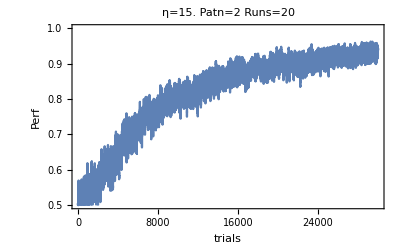

```mathematica
PlotPerfInFile[iter,eta,"OnlineRuleAMPA_Origin_T100"]
```

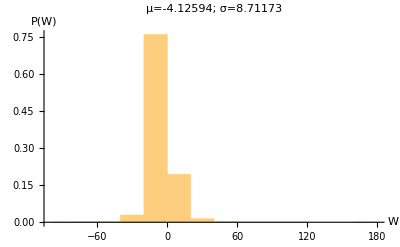

```mathematica
PlotWeightsInFile[iter,eta,"OnlineRuleAMPA_Origin_T100"]
```

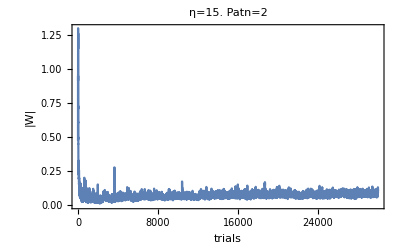

```mathematica
PlotWEvolInFile[iter,eta,"OnlineRuleAMPA_Origin_T100",0.2]
```

```mathematica
StatActInFile[iter,eta,"OnlineRuleAMPA_Origin_T100"]
```

{0.,0.95}

{0.,0.9}

{0.,0.8}

{0.05,0.9}

{0.,0.7}

{0.,0.95}

{0.,0.4}

{0.,0.8}

{0.,0.7}

{0.,0.8}

{0.,0.7}

{0.,0.85}

{0.,0.95}

{0.,0.75}

{0.05,0.8}

{0.,0.85}

{0.,0.9}

{0.,0.75}

{0.,0.75}

{0.,0.65}

{0.89375,{0.005,0.7925}}

```mathematica
StatActInFilePreLearning[iter,eta,"OnlineRuleAMPA_Origin_T100"]
```

Mean activity ((00),(10),(01),(11))

{1.68132,2.30275}

{0.648352,0.623853}

```mathematica
GetFinalStatFromFile[iter,eta,"OnlineRuleAMPA_Origin_T100"]
```

{2.49658,,}

#### comparison perf

```mathematica
names50A={getFileName[10.,30000,"OnlineRuleAMPA_Origin_T100"],getFileName[15.,30000,"OnlineRuleAMPA_Origin_T100"],getFileName[22.5,30000,"OnlineRuleAMPA_Origin_T100"]};
```

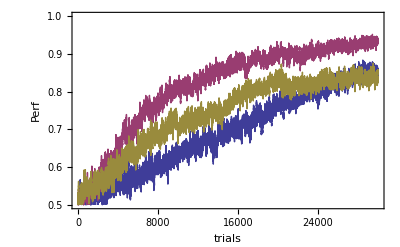

```mathematica
PlotPerfInFile[names50A,{"η=10.","η=15","η=22.5"}]
```

### Plot example after learning (Toverlap=10 and η =15)

#### ini

```mathematica
BS=22;
```

```mathematica
OptPad1={{38,20},{3,2}};
```

```mathematica
OptPad2={{38,20},{27,2}};
```

```mathematica
Inp[t_,X_,func_] :=
 (* add up the various spikes defined by <func> *)
Apply[Plus,
 func[
(* delete the negative times *)
 DeleteCases [t-X, a_/; a <0 ,{-1}]] ,
{1}(* only at the first level*) ];
```

```mathematica
myNMDA[t_] := Block[ {tNMDA=50}, 
  UnitStep[t]-UnitStep[t-tNMDA]]
NMDA[t_]:=UnitStep[t]-UnitStep[t-tNMDA];
```

```mathematica
gFileName=getFileName[15,30000,"OnlineRuleAMPA_Origin_T100"]
```

./out/_eta15._trials30000_IL100_NbNeurons20_USpike0.4_SigmaW3.4_UrS-1_aAMPA0.0632455_Tolp10_OnlineRuleAMPA_Origin_T100.out

```mathematica
res=ReadList[gFileName];
```

```mathematica
Seedtab=res/.trialDT[_,_,_,_,outDT[a_],_]->a;
```

```mathematica
WTab=res/.trialDT[_,_,_,outDT[a_],_,_]->a;
```

```mathematica
k=17;
```

```mathematica
SeedRandom[Seedtab[[k]]];
{wwin,Mask} = myiniws[0.,σW,nbNeuron,0.5];
Clear[Patsepsps];
Patsepsps[x1_,x2_]:=Patsepsps[x1,x2]=Patsepsps0[x1,x2];
```

```mathematica
stim=1. Table[ 
Map[getActAff[#,d]&,Itimes]
,{d,{-1,1}}];
```

```mathematica
wf=WTab[[k]];
```

#### stim[[1]]

```mathematica
SeedRandom[26];
```

```mathematica
aAMPA=Round[N[0.2/Sqrt[nbNeuron*pConnect]],0.00000001];stepperlist=1;{last,{Y,Z}}=nextpassEpisode[stim[[1]],ini[wf]];stepperlist=0;
```

```mathematica
Z
```

{}

```mathematica
Y
```

{{},{32,50},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{134,136,139,140,141,144,145,146,148,150,153,154,156,159,162,163,164,165,166,167,168,169,170,171,172,174,175,177,179,180,181,182,183,184,185,189,191,192,194,196,197,198,200,201,202,203,204,206,207,212,214,215}}

```mathematica
Total@Map[Sign@Length[#]&,Y]
```

2

```mathematica
resStep=Transpose@Most@Most@last;
```

```mathematica
USoma=resStep[[1]];
```

```mathematica
USoma[[Z]]=1.;
```

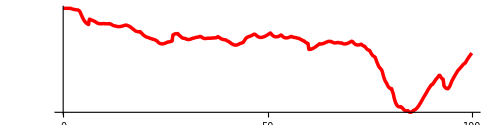

```mathematica
figUSomaTimeCourse=ListLinePlot[USoma,PlotRange->All,PlotStyle->{Red,Thickness[0.005]},(*Axes->None,*)DataRange->{0,Tonl},PlotRange->All,Ticks->{{0,{50,"50"},100},{0}},BaseStyle->BS,LabelStyle->(FontFamily->"Helvetica"),AxesStyle->{Thick,Arrowheads[{0.05}]},AspectRatio->0.25,ImagePadding->OptPad1,ImageSize->500]
```

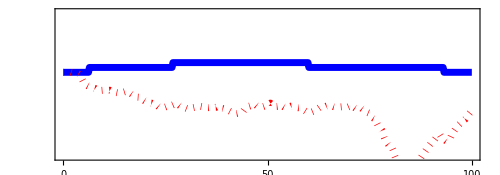

```mathematica
figUSomaTimeCourse=ListLinePlot[{ resStep[[3]],resStep[[4]]},Joined->True,Frame->True,Axes->False,ImageSize->500,BaseStyle->BS,LabelStyle->(FontFamily->"Helvetica"),DataRange->{0,100},PlotRange->{-7,5},PlotStyle->{{Blue,Thickness[0.01]},{Red,Dotted,Thickness[0.01]},{Red,Dashed,Thickness[0.01]}},FrameTicks->{ {0,50,100},(*{-15,0,4}*)None, (*{{0,"θ_S"}}*)None, None},AspectRatio->0.35,ImagePadding->OptPad2]
```

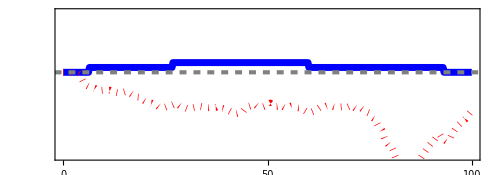

```mathematica
figUSomaTimeCourse=Show[figUSomaTimeCourse,Graphics[{Gray,Dashed,Thickness[.006],Line[{{-1000,0},{40000,0}}]}],ImagePadding->OptPad2]
```

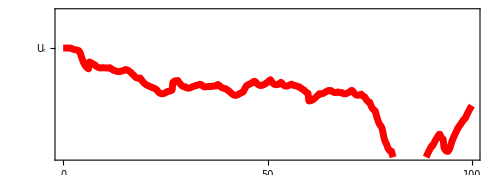

```mathematica
figUSomaTimeCourse=ListLinePlot[USoma,Joined->True,Frame->True,Axes->False,ImageSize->500,BaseStyle->BS,LabelStyle->(FontFamily->"Helvetica"),DataRange->{0,100},PlotRange->{-7,1},PlotStyle->{{Red,Thickness[0.01]},{Red,Dotted,Thickness[0.01]},{Red,Dashed,Thickness[0.01]}},FrameTicks->{ {0,50,100},{{UrestSoma,"U_r"}}, {{0,"θ_S"}}, None},AspectRatio->0.35,ImagePadding->OptPad2]
```

```mathematica
NMDA[t_]:=UnitStep[t]-UnitStep[t-tNMDA]
```

```mathematica
Itimes2=Range[0,100,1];
```

```mathematica
NMDAs[X_] :=Map[Inp[#,X,NMDA]&,Itimes2];
```

```mathematica
NMDAYt=Transpose@Take[NMDAs[step Y],Round[Tonl]];
```

```mathematica
NMDAYt=Map[If[#>0,Min[#,1],None]&,NMDAYt,{2}];
```

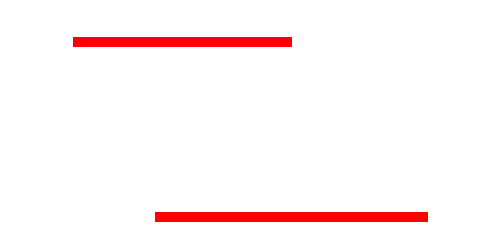

```mathematica
figDendAct=ArrayPlot[NMDAYt,AspectRatio->0.5,ImageSize->500,DataRange->{{1,Tonl},{1,20}},PlotRange->{{1,100},{0,21}},FrameTicks->{{{1,10,20},None},{{1,50,100},None}},BaseStyle->BS,ImagePadding->OptPad2,LabelStyle->(FontFamily->"Helvetica"),Background->None,ColorRules->{1->{Opacity[0.5],Red}}(*ColorFunction->(If[#>0.1,{Opacity[0.5],Green},None]&)*)]
```

```mathematica
UDen=Transpose@Map[Flatten,resStep[[2]]];
```

```mathematica
maxUDen=Max@UDen
```

6.3808

```mathematica
minUDen=Min@UDen
```

-13.1648

```mathematica
maxUDen=7;
```

```mathematica
minUDen=-10;
```

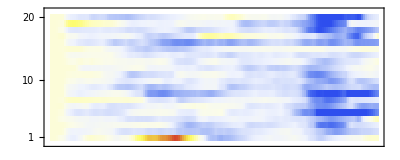

```mathematica
figUDen=MatrixPlot[((UDen-minUDen)/(maxUDen-minUDen)),ImageSize->400,DataRange->{{1,Tonl},{1,20}},PlotRange->{{1,100},{0,21}},FrameTicks->{{{1,10,20},None},{None(*{1,250,500}*),None}},BaseStyle->BS,AspectRatio->0.4,ImagePadding->{{40,27},{28,3}},LabelStyle->(FontFamily->"Helvetica"),ColorFunctionScaling->False,ColorFunction->ColorData["TemperatureMap"],
FrameStyle->Directive[Thickness[0.01],Darker@Green],FrameTicksStyle->Black]
```

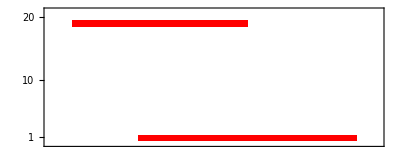

```mathematica
figDendActF=Show[figUDen,figDendAct]
```

```mathematica
Export["figDirSel-1_DendAct.png",figDendActF];
```

```mathematica
Zpts=Map[{{#,0},{#,1},{#,0}}&,step If[Length@Z>0,Z,{-1000}]]
```

{{{-200.,0},{-200.,1},{-200.,0}}}

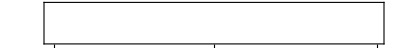

```mathematica
figSomActF=ListLinePlot[Zpts,PlotStyle->Map[{Red,Thickness[.01]}&,Zpts],PlotRange->{{0,100},{0,1}},FrameTicks->{{None,None},{{1,50,100},None}},Joined->True,Frame->True,Axes->False,BaseStyle->BS,LabelStyle->(FontFamily->"Helvetica"),AspectRatio->0.05,ImageSize->400,ImagePadding->{{40,27},{28,3}},
FrameStyle->Directive[Thickness[0.01],Darker@Green],FrameTicksStyle->Black
]
```

```mathematica
Export["figDirSel-1_SomAct.png",figSomActF];
```

#### stim[[2]]

```mathematica
SeedRandom[26];
```

```mathematica
aAMPA=Round[N[0.2/Sqrt[nbNeuron*pConnect]],0.00000001];stepperlist=1;{last,{Y,Z}}=nextpassEpisode[stim[[2]],ini[wf]];stepperlist=0;
```

```mathematica
Z
```

{24,35,43}

```mathematica
Y
```

{{22,23,24,25,28,30,31,33,34,36,37,38,39,40,41,43,44,45,46,48,49,50,52,57,58,59,60,63,64,66,70,71,73,74,77,78,79,81,82,84,85,87,91,92,93,94},{40,42,43,47,48,50,51,52,53,54,56,58,59,60,62,63,64,65,67,68,69,71,73,74,75,76,77,79,81,84,86,90,91},{},{13,16,17,18,19,25},{},{},{},{},{},{},{},{22,23,24,25,26,27,29,30,31,33,35,36,37,38,40,41,42,45,46,47,48,49,50,53,54,58,59,61,62,63},{41},{72,75},{},{34,51,57,58,60,66},{25,28,36,38,39,43},{},{},{363,364,365,367,369,370,371,372,374,376,377,378,381,383}}

```mathematica
resStep=Transpose@Most@Most@last;
```

```mathematica
USoma=resStep[[1]];
```

```mathematica
USoma[[Z]]=1.;
```

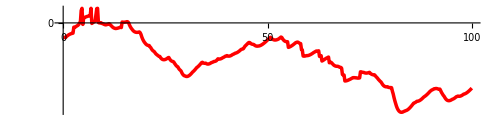

```mathematica
figUSomaTimeCourse=ListLinePlot[USoma,PlotRange->All,PlotStyle->{Red,Thickness[0.005]},(*Axes->None,*)DataRange->{0,Tonl},PlotRange->All,Ticks->{{0,{50,"50"},100},{0}},BaseStyle->BS,LabelStyle->(FontFamily->"Helvetica"),AxesStyle->{Thick,Arrowheads[{0.05}]},AspectRatio->0.25,ImagePadding->OptPad1,ImageSize->500]
```

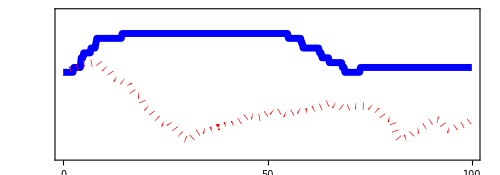

```mathematica
figUSomaTimeCourse=ListLinePlot[{ resStep[[3]],resStep[[4]]},Joined->True,Frame->True,Axes->False,ImageSize->500,BaseStyle->BS,LabelStyle->(FontFamily->"Helvetica"),DataRange->{0,100},PlotRange->{-7,5},PlotStyle->{{Blue,Thickness[0.01]},{Red,Dotted,Thickness[0.01]},{Red,Dashed,Thickness[0.01]}},FrameTicks->{ {0,50,100},(*{-15,0,4}*)None, (*{{0,"θ_S"}}*)None, None},AspectRatio->0.35,ImagePadding->OptPad2]
```

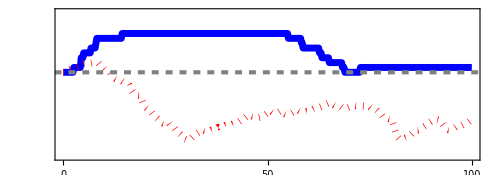

```mathematica
figUSomaTimeCourse=Show[figUSomaTimeCourse,Graphics[{Gray,Dashed,Thickness[.006],Line[{{-1000,0},{40000,0}}]}],ImagePadding->OptPad2]
```

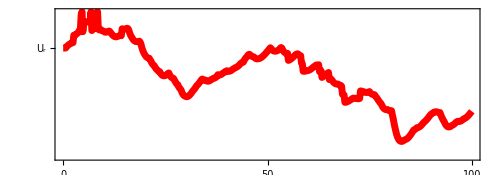

```mathematica
figUSomaTimeCourse=ListLinePlot[USoma,Joined->True,Frame->True,Axes->False,ImageSize->500,BaseStyle->BS,LabelStyle->(FontFamily->"Helvetica"),DataRange->{0,100},PlotRange->{-7,1},PlotStyle->{{Red,Thickness[0.01]},{Red,Dotted,Thickness[0.01]},{Red,Dashed,Thickness[0.01]}},FrameTicks->{ {0,50,100},{{UrestSoma,"U_r"}}, {{0,"θ_S"}}, None},AspectRatio->0.35,ImagePadding->OptPad2]
```

```mathematica
Itimes2=Range[0,100,1];
```

```mathematica
NMDAs[X_] :=Map[Inp[#,X,NMDA]&,Itimes2];
```

```mathematica
NMDAYt=Transpose@Take[NMDAs[step Y],Round[Tonl]];
```

```mathematica
NMDAYt=Map[If[#>0,Min[#,1],None]&,NMDAYt,{2}];
```

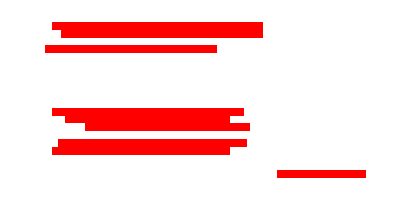

```mathematica
figDendAct=ArrayPlot[NMDAYt,AspectRatio->0.5,ImageSize->400,DataRange->{{1,Tonl},{1,20}},PlotRange->{{1,100},{0,21}},FrameTicks->{{{1,10,20},None},{{1,50,100},None}},BaseStyle->BS,ImagePadding->OptPad2,LabelStyle->(FontFamily->"Helvetica"),Background->None,ColorRules->{1->{Opacity[0.5],Red}}(*ColorFunction->(If[#>0.1,{Opacity[0.5],Green},None]&)*)]
```

```mathematica
UDen=Transpose@Map[Flatten,resStep[[2]]];
```

```mathematica
maxUDen=Max@UDen
```

8.18585

```mathematica
minUDen=Min@UDen
```

-10.123

```mathematica
maxUDen=7;
```

```mathematica
minUDen=-10;
```

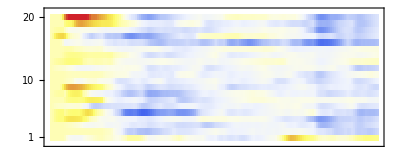

```mathematica
figUDen=MatrixPlot[((UDen-minUDen-UrestSoma)/(maxUDen-minUDen)),ImageSize->400,DataRange->{{1,Tonl},{1,20}},PlotRange->{{1,100},{0,21}},FrameTicks->{{{1,10,20},None},{None(*{1,250,500}*),None}},BaseStyle->BS,AspectRatio->0.4,ImagePadding->{{40,27},{28,3}},LabelStyle->(FontFamily->"Helvetica"),ColorFunctionScaling->False,ColorFunction->ColorData["TemperatureMap"],
FrameStyle->Directive[Thickness[0.01],Red],FrameTicksStyle->Black]
```

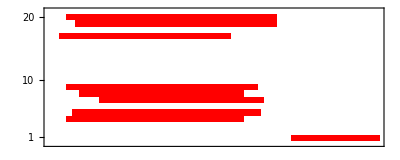

```mathematica
figDendActF=Show[figUDen,figDendAct]
```

```mathematica
Export["figDirSel1_DendAct.png",figDendActF];
```

```mathematica
Zpts=Map[{{#,0},{#,1},{#,0}}&,step If[Length@Z>0,Z,{-1000}]]
```

{{{4.8,0},{4.8,1},{4.8,0}},{{7.,0},{7.,1},{7.,0}},{{8.6,0},{8.6,1},{8.6,0}}}

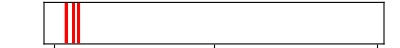

```mathematica
figSomActF=ListLinePlot[Zpts,PlotStyle->Map[{Red,Thickness[.005]}&,Zpts],PlotRange->{{0,100},{0,1}},FrameTicks->{{None,None},{{1,50,100},None}},Joined->True,Frame->True,Axes->False,BaseStyle->BS,LabelStyle->(FontFamily->"Helvetica"),AspectRatio->0.05,ImageSize->400,ImagePadding->{{40,27},{28,3}},
FrameStyle->Directive[Thickness[0.01],Red],FrameTicksStyle->Black]
```

```mathematica
Export["figDirSel1_SomAct.png",figSomActF];
```

## R-STDP(dendritic spikes-PSPs)

#### code

```mathematica
σW=3.;
```

```mathematica
{Ap,An,τp,τn}={0.188,0(*-0.094/2*),10.,20.}
```

```mathematica
stepper =
InlComp[
{mempots,spikegenNMDA,incrBuff,myUnitStep,ϕN,ϕS,k2,DϕN,DlϕN,DϕS,DlϕS,Tonl,step,stNMDA,tNMDA,Urest,β2,tmrsfac,tmrini,αg,βg,γg,αl,βl,γl,UmaxSoma,τfrac,τInhib,Ap,An,τp,τn,τs,τm,spikegenPreSyn},
{{myinps,_Real,2},   (* input rates *)
{myw,_Real,2},(* weights for the "dendritic neurons" and AMPA synapses for the first component*)
{resets,_Integer,1}, (* the NMDA spike response *)
{reset,_Real}, (* the reset kernel for the soma *)
{ETr,_Real,2}, (* the eligibility trace *)
{APBuff,_Real,1}, (* mmemory of the AP *)
{PSPBuff,_Real,1} (* memory of the pre-synaptic spikes *)
},
Block[ {uSoma (*membrane potential at the soma *),ud, ntUpd,thisinp,spikesNMDA,SpikeSoma,us,nw,i,len,istepperlist,mask,nmyresets,nmyreset,nBufUpd ,inRefPer,nUspikeNMDA,κ,ntNMDASpBuff,EligSoma,ntPSPBuff,intRefdendStruct,myET,indBuff=0,NMDASpikeCounts,θMultSpike=(1.15),nmBuffSyn,uTmp,DendStruct,nmyinps,naAMPA,PSPm,PSPs,spikesPre},

(*local compy to change of context only at the begining*)
nmyinps=myinps;
PSPm=0.0*First[nmyinps];
PSPs=0.0*PSPm;
spikesPre=PSPs;
mask = Mask;
naAMPA=aAMPA;
nUspikeNMDA=UspikeNMDA;
κ=N[k2*(Exp[β2*nUspikeNMDA]-1.)];
len = Round[Tonl/step];
istepperlist = stepperlist;
myET=(*0.0**)ETr;
nw = myw;
nmyresets =(*0.0**)resets (*Table[0,{Length@nw}]*);
intRefdendStruct= nmyresets*0-stNMDA;
inRefPer=Table[0.,{Length@nw}];
DendStruct=Table[{1.},{Length@nw}];
NMDASpikeCounts=inRefPer;
EligSoma=inRefPer;
nmyreset=(*0.**)reset;
ntNMDASpBuff=(*0.0**)APBuff(*Updinc*);(* memory of the state of the synapses when a NMDA spike occurs*)
(*represent the 50ms low pass filter of the no spiking part of Pfister ET*)
(*nBufUpd = PSPBuff*)(* Table[ntUpd,{stNMDA}]*);(* buffer for e^iv *)
ntPSPBuff=PSPBuff; 
ntUpd=0.0*nw;
uSoma=0.;
EligSoma=inRefPer;
uTmp=inRefPer;


For[i=1, i≤len,i++,
(*indBuff=incrBuff[indBuff];*)
nmyresets = nmyresets+1; (* refractoriness period *)
inRefPer=0.5(Sign[nmyresets-0.1] +1.) ;(* determine the sign of the  attenuation integral *)

spikesPre=spikegenPreSyn[nmyinps[[i]]];
PSPm=spikesPre+(1.0-step/τm)PSPm;
PSPs=spikesPre+(1.0-step/τs)PSPs;
thisinp ={(PSPm-PSPs)/(τm-τs)};   (* vector of inputs as a matrix *)


ud= mempots[nw,thisinp] ; (* calculate the membrane potential in the dendritic branchs ("line vector") *)
spikesNMDA= spikegenNMDA[ud(*,inRefPer*)]; (* calculate the NMDA spikes *)
uSoma=nUspikeNMDA*Total[1.-inRefPer]-nmyreset+Urest+naAMPA*Total[Flatten@ud-Urest];
nmyreset = nmyreset  tmrsfac;
NMDASpikeCounts=NMDASpikeCounts*(1.0-step/tNMDA);

SpikeSoma=0.5+0.5*Sign[1-Exp[-(step * ϕS[uSoma])]-RandomReal[{0,1}]];
(* somatic spike *)
If[SpikeSoma==1.0,
nmyreset+=tmrini;
Sow[ i];
];

ntNMDASpBuff=(1.0-step/τn)ntNMDASpBuff;
ntPSPBuff=Ap/τp*spikesPre+(1.0-step/τp)ntPSPBuff;
ntUpd=0.ntUpd;
(* NMDA spikes *)
If [spikesNMDA ≠ {0} ,(
ntUpd[[spikesNMDA ]]  =DendStruct[[spikesNMDA ]] .{ntPSPBuff};
ntNMDASpBuff[[spikesNMDA ]] +=An/τn;
nmyresets[[spikesNMDA ]] = intRefdendStruct[[spikesNMDA ]];
Sow[ i,spikesNMDA];
us = ud[[spikesNMDA]];
)];

ntUpd +=((DendStruct ntNMDASpBuff).{spikesPre});
myET=ntUpd+(1.0-step/(τfrac*Tonl))myET;

If[(istepperlist==1 ),
Sow[{uSoma,ud,nUspikeNMDA*Total[1.-inRefPer],naAMPA*Total[Flatten@ud-Urest]},"ReturnValue"];
];

];
Sow[{uSoma,ud,0.0,0.0},"ReturnValue"];
Sow[{nw,nmyresets,nmyreset,myET,ntNMDASpBuff,ntPSPBuff},"ReturnValue"];
],
{{Mask,_Real,2},{UspikeNMDA,_Real},{stepperlist,_Integer},{aAMPA,_Real},{Position[_, 1],_Integer,2}}
];
```

#### simulation

```mathematica
eta=1.;
```

```mathematica
iter=30000;
```

```mathematica
Table[Print@Timing@learnInFile[iter,0,eta,"OnlineNMDASTDP_Origin_T100"],{20}];
```

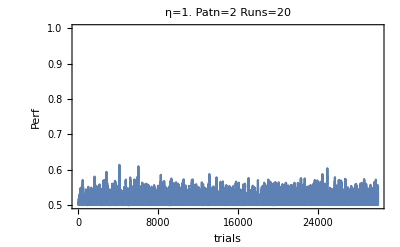

```mathematica
PlotPerfInFile[iter,eta,"OnlineNMDASTDP_Origin_T100"]
```

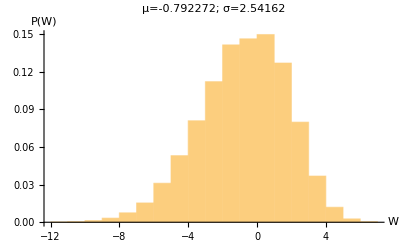

```mathematica
PlotWeightsInFile[iter,eta,"OnlineNMDASTDP_Origin_T100"]
```

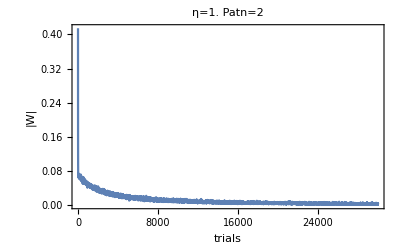

```mathematica
PlotWEvolInFile[iter,eta,"OnlineNMDASTDP_Origin_T100",0.2]
```

```mathematica
StatActInFile[iter,eta,"OnlineNMDASTDP_Origin_T100"]
```

{0.,0.}

{0.,0.}

{0.,0.}

«17 more identical outputs»

{0.5,{0.,0.}}

```mathematica
StatActInFilePreLearning2[fileN_]:=Block[{tmp,tmp2,res,wwin,Seedtab,WTab,k,x1,x2,last,Y,Z,nbSample=20,totalRuns,stim},
res=ReadList[fileN];
totalRuns=Length@res;
WTab=res/.trialDT[_,_,_,outDT[a_],_,_]->a;
Seedtab=res/.trialDT[_,_,_,_,outDT[a_],_]->a;

stim=1. Table[ 
Map[getActAff[#,d]&,Itimes]
,{d,{-1,1}}];

res=Transpose@Table[
SeedRandom[Seedtab[[k]]];
{wwin,Mask} = myiniws[0,σW,nbNeuron,pConnect];

Table[
Table[
{last,{Y,Z}}=nextpassEpisode[stim[[p]],ini[(*tmp*)wwin]];
(*1-Abs[Sign@Length@Flatten@Z-Mod[x1+x2,2]]*)
1.-Abs[(p-1)-Sign@Length@Flatten@Z]
,{nbSample}]
,{p,2}]
,{k,totalRuns}];
{{N@Mean@Flatten[res],N@StandardDeviation@Flatten[res]/Sqrt[Patn totalRuns-1]},Map[{N@Mean@Flatten[#],N@StandardDeviation@Flatten[#]/Sqrt[totalRuns-1]}&,res]}
];
```

```mathematica
OptPadding={{42,26},{29,9}};
```

```mathematica
{PerfIni,PerfsIni}=StatActInFilePreLearning2[getFileName[1.,30000,"OnlineNMDASTDP_Origin_T100"]]
```

{{0.50875,0.0801019},{{0.2575,0.100439},{0.76,0.0981023}}}

```mathematica
FileNameDirSel=getFileName[1.,30000,"OnlineNMDASTDP_Origin_T100"];
```

```mathematica
rest=ReadList[FileNameDirSel];
```

```mathematica
rest=Take[rest,20];
```

```mathematica
PerfGlob=rest/.trialDT[outDT[a_],_,_,_,_,_]->a;
```

```mathematica
PerfGlob=Map[λFilter[#,0.2/Patn]&,PerfGlob];
```

```mathematica
GlobRange={1}~Join~Range[3250,28000,3000]~Join~{30000};ErrorPtsGlob=(*{{{1,PerfIni[[1]]},ErrorBar[PerfIni[[2]]]}}~Join~*)MapThread[{{#3,#1},ErrorBar[#2]}&,{(Mean@PerfGlob)[[GlobRange]],(StandardDeviation@PerfGlob/Sqrt[Length@PerfGlob-1])[[GlobRange]],GlobRange}];
```

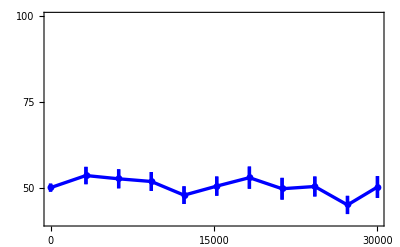

```mathematica
OptPadding={{40,27},{28,8}};
PlotPerfDirSel=ErrorListPlot[{ErrorPtsGlob},Joined->True,Frame->True,Axes->False,ImageSize->400,FrameTicks->{ {0,15000,30000},{  {0.5,50},{0.75,75},{1.,100}}, None, None},BaseStyle->22,LabelStyle->(FontFamily->"Helvetica"),(*FrameLabel->{"trials","Performance (%)"},*)PlotRange->{0.40,1},PlotStyle->{{Blue,Thickness[0.006]},{Red,Thickness[0.006]},{Darker@Green,Thickness[0.006]}},PlotMarkers->Automatic,ImagePadding->OptPadding]
```

## R - STDP (APs - PSPs)

#### code

```mathematica
σW=3.;
```

```mathematica
{Ap,An,τp,τn}={0.188,0(*-0.094/2*),10.,20.};
```

```mathematica
stepper =
InlComp[
{mempots,spikegenNMDA,incrBuff,myUnitStep,ϕN,ϕS,k2,DϕN,DlϕN,DϕS,DlϕS,Tonl,step,stNMDA,tNMDA,Urest,β2,tmrsfac,tmrini,αg,βg,γg,αl,βl,γl,UmaxSoma,τfrac,Ap,An,τp,τn,τs,τm,spikegenPreSyn},
{{myinps,_Real,2},   (* input rates *)
{myw,_Real,2},(* weights for the "dendritic neurons" and AMPA synapses for the first component*)
{resets,_Integer,1}, (* the NMDA spike response *)
{reset,_Real}, (* the reset kernel for the soma *)
{ETr,_Real,2}, (* the eligibility trace *)
{APBuff,_Real}, (* mmemory of the AP *)
{PSPBuff,_Real,1} (* memory of the pre-synaptic spikes *)
},
Block[ {uSoma (*membrane potential at the soma *),ud, ntUpd,thisinp,spikesNMDA,SpikeSoma,us,nw,i,len,istepperlist,mask,nmyresets,nmyreset,nBufUpd ,inRefPer,nUspikeNMDA,κ,ntAPBuff,EligSoma,ntPSPBuff,intRefdendStruct,myET,indBuff=0,NMDASpikeCounts,θMultSpike=(1.15),nmBuffSyn,uTmp,DendStruct,nmyinps,naAMPA,PSPm,PSPs,spikesPre},

(*local compy to change of context only at the begining*)
nmyinps=myinps;
PSPm=0.0*First[nmyinps];
PSPs=0.0*PSPm;
spikesPre=PSPs;
mask = Mask;
naAMPA=aAMPA;
nUspikeNMDA=UspikeNMDA;
κ=N[k2*(Exp[β2*nUspikeNMDA]-1.)];
len = Round[Tonl/step];
istepperlist = stepperlist;
myET=(*0.0**)ETr;
nw = myw;
nmyresets =(*0.0**)resets (*Table[0,{Length@nw}]*);
intRefdendStruct= nmyresets*0-stNMDA;
inRefPer=Table[0.,{Length@nw}];
DendStruct=Table[{1.},{Length@nw}];
NMDASpikeCounts=inRefPer;
EligSoma=inRefPer;
nmyreset=(*0.**)reset;
ntAPBuff=(*0.0**)APBuff(*Updinc*);(* memory of the state of the synapses when a NMDA spike occurs*)
(*represent the 50ms low pass filter of the no spiking part of Pfister ET*)
(*nBufUpd = PSPBuff*)(* Table[ntUpd,{stNMDA}]*);(* buffer for e^iv *)
ntPSPBuff=PSPBuff; 
ntUpd=0.0*ntPSPBuff;
uSoma=0.;
EligSoma=inRefPer;
uTmp=inRefPer;


For[i=1, i≤len,i++,
(*indBuff=incrBuff[indBuff];*)
nmyresets = nmyresets+1; (* refractoriness period *)
inRefPer=0.5(Sign[nmyresets-0.1] +1.) ;(* determine the sign of the  attenuation integral *)

spikesPre=spikegenPreSyn[nmyinps[[i]]];
PSPm=spikesPre+(1.0-step/τm)PSPm;
PSPs=spikesPre+(1.0-step/τs)PSPs;
thisinp ={(PSPm-PSPs)/(τm-τs)};   (* vector of inputs as a matrix *)


ud= mempots[nw,thisinp] ; (* calculate the membrane potential in the dendritic branchs ("line vector") *)
spikesNMDA= spikegenNMDA[ud(*,inRefPer*)]; (* calculate the NMDA spikes *)
uSoma=nUspikeNMDA*Total[1.-inRefPer]-nmyreset+Urest+naAMPA*Total[Flatten@ud-Urest];
nmyreset = nmyreset  tmrsfac;
NMDASpikeCounts=NMDASpikeCounts*(1.0-step/tNMDA);

SpikeSoma=0.5+0.5*Sign[1-Exp[-(step * ϕS[uSoma])]-RandomReal[{0,1}]];
(* somatic spike *)
If[SpikeSoma==1.0,
nmyreset+=tmrini;
Sow[ i];
];
ntAPBuff=An/τn SpikeSoma+(1.0-step/τn)ntAPBuff;
ntPSPBuff=Ap/τp*spikesPre+(1.0-step/τp)ntPSPBuff;

ntUpd =(spikesPre*ntAPBuff)+(SpikeSoma*ntPSPBuff);


(* NMDA spikes *)
If [spikesNMDA ≠ {0} ,(
nmyresets[[spikesNMDA ]] = intRefdendStruct[[spikesNMDA ]];
Sow[ i,spikesNMDA];
us = ud[[spikesNMDA]];
)];

myET=(DendStruct.{ntUpd})+(1.0-step/(τfrac*Tonl))myET;

If[(istepperlist==1 ),
Sow[{uSoma,ud,nUspikeNMDA*Total[1.-inRefPer],naAMPA*Total[Flatten@ud-Urest]},"ReturnValue"];
];

];
Sow[{uSoma,ud,0.0,0.0},"ReturnValue"];
Sow[{nw,nmyresets,nmyreset,myET,ntAPBuff,ntPSPBuff},"ReturnValue"];
],
{{Mask,_Real,2},{UspikeNMDA,_Real},{stepperlist,_Integer},{aAMPA,_Real},{Position[_, 1],_Integer,2}}
];
```

#### simulation

```mathematica
eta=1.;
```

```mathematica
iter=30000;
```

```mathematica
Table[Print@Timing@learnInFile[iter,0,eta,"OnlineSTDP_Origin_T100_fl5"],{20}];
```

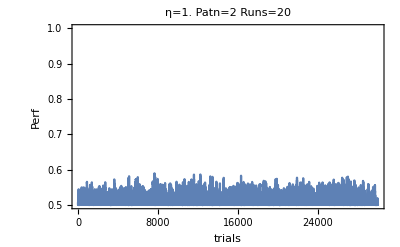

```mathematica
PlotPerfInFile[iter,eta,"OnlineSTDP_Origin_T100_fl5"]
```

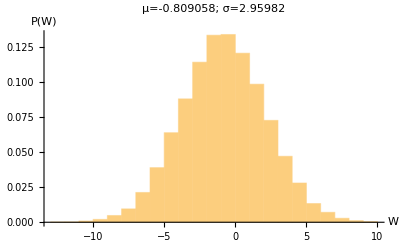

```mathematica
PlotWeightsInFile[iter,eta,"OnlineSTDP_Origin_T100_fl5"]
```

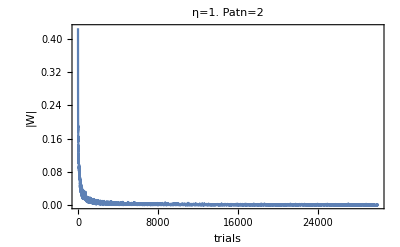

```mathematica
PlotWEvolInFile[iter,eta,"OnlineSTDP_Origin_T100_fl5",0.2]
```

```mathematica
StatActInFile[iter,eta,"OnlineSTDP_Origin_T100_fl5"]
```

{0.,0.}

{0.,0.}

{0.,0.}

«5 more identical outputs»

{0.,0.05}

{0.,0.05}

{0.,0.}

{0.,0.}

{0.,0.}

«1 more identical outputs»

{0.05,0.}

{0.,0.}

{0.,0.}

{0.,0.}

«2 more identical outputs»

{0.50125,{0.0025,0.005}}

```mathematica
StatActInFilePreLearning[iter,eta,"OnlineSTDP_Origin_T100_fl5"]
```

Mean activity ((00),(10),(01),(11))

{3.02941,3.40816}

{0.823529,0.806122}

```mathematica
GetFinalStatFromFile[iter,eta,"OnlineSTDP_Origin_T100_fl5"]
```

```mathematica
OptPadding={{42,26},{29,9}};
```

```mathematica
{PerfIni,PerfsIni}=StatActInFilePreLearning2[getFileName[1.,30000,"OnlineSTDP_Origin_T100_fl5"]]
```

{{0.49,0.0800981},{{0.2175,0.0947629},{0.7625,0.0977504}}}

```mathematica
FileNameDirSel=getFileName[1.,30000,"OnlineSTDP_Origin_T100_fl5"];
```

```mathematica
rest=ReadList[FileNameDirSel];
```

```mathematica
rest=Take[rest,20];
```

```mathematica
PerfGlob=rest/.trialDT[outDT[a_],_,_,_,_,_]->a;
```

```mathematica
PerfGlob=Map[λFilter[#,0.2/Patn]&,PerfGlob];
```

```mathematica
GlobRange={1}~Join~Range[2790,28000,3000]~Join~{30000};ErrorPtsGlob=(*{{{1,PerfIni[[1]]},ErrorBar[PerfIni[[2]]]}}~Join~*)MapThread[{{#3,#1},ErrorBar[#2]}&,{(Mean@PerfGlob)[[GlobRange]],(StandardDeviation@PerfGlob/Sqrt[Length@PerfGlob-1])[[GlobRange]],GlobRange}];
```

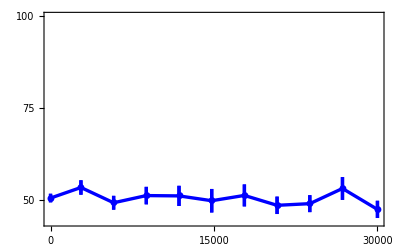

```mathematica
OptPadding={{40,27},{28,8}};
PlotPerfDirSel=ErrorListPlot[{ErrorPtsGlob},Joined->True,Frame->True,Axes->False,ImageSize->400,FrameTicks->{ {0,15000,30000},{  {0.5,50},{0.75,75},{1.,100}}, None, None},BaseStyle->22,LabelStyle->(FontFamily->"Helvetica"),(*FrameLabel->{"trials","Performance (%)"},*)PlotRange->{0.44,1},PlotStyle->{{Blue,Thickness[0.006]},{Red,Thickness[0.006]},{Darker@Green,Thickness[0.006]}},PlotMarkers->Automatic,ImagePadding->OptPadding]
```